```mathematica
BaseName = "2_00";
SignalNames = {"2_01", "2_02", "2_03", "2_04", "2_05", "2_06", "2_07", "2_08"};
path = "D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_2\\";
```

```mathematica
base=  Flatten[Import[path<>BaseName<>".csv"]]⟦3200;;5500⟧;
signals = Map[(Flatten@Import[path<>#<>".csv"])⟦3200;;5500⟧&, SignalNames];
```

```mathematica
GetListPlot[dots_] := ListPlot[dots, PlotRange->Full, Joined->True, GridLines->Automatic];
```

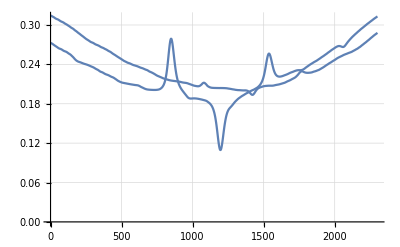

```mathematica
Show[{
GetListPlot[signals⟦1⟧],
GetListPlot[signals⟦8⟧]
}]
```

b+a (x-x0)^2

{a→7.59878×10^-8,x0→1146.89,b→0.192461}

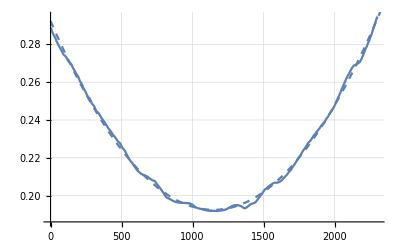

```mathematica
f = a(x-x0)^2+b
par = FindFit[base, f, {a, x0, b}, x]
Show[{
GetListPlot[base ],
Plot[(f /. par), {x, 0, 2500}, PlotStyle->Dashed]
}]
```

```mathematica
aVal = 7.86189 10^-8;
GetPars[y_] := Module[{dots},
f = aVal(x-x0)^2+b;
dots = y;
par = FindFit[dots, f, {x0, b}, x];
{Round[x0 /. par, 1], (b /. par)}
];
ShiftDots[dots_] := Module[{x0, b, dots2, Δ},
{x0, b} = GetPars[dots];
dots2 = Transpose@{Range[1, Length@dots, 1], dots};
dots2⟦;;,1⟧=dots2⟦;;,1⟧-x0;
dots2⟦;;,2⟧=dots2⟦;;,2⟧-b-aVal dots2⟦;;,1⟧^2;
Δ = dots2⟦Ordering[dots2⟦;;,2⟧,1], 1⟧⟦1⟧;
dots2⟦;;,1⟧=dots2⟦;;,1⟧-Δ;
dots2
];
```

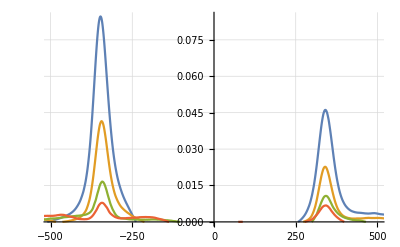

```mathematica
ListPlot[{
ShiftDots[ signals⟦1⟧], ShiftDots[ signals⟦4⟧],
ShiftDots[ signals⟦7⟧], ShiftDots[ signals⟦8⟧]
}, Joined->True, PlotRange->{{-500, 500}, {0, Full}}, GridLines->{Automatic, Range[-0.1, 0.1, 10^-2/2]}]
```

```mathematica
0.085/0.045
0.041 / 0.022
0.015 / 0.01
```

1.88889

1.86364

1.5

{x0→1252.08,b→0.201786}

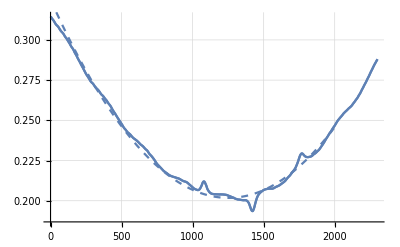

ListPlot::lpn: dots0 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[dots0,PlotRange→Full,Joined→True,GridLines→Automatic]}].

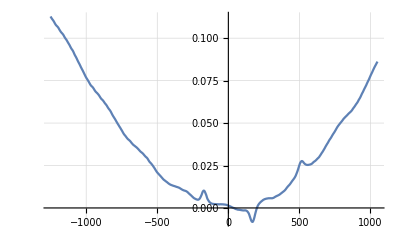
Show[{-Graphics-,ListPlot[dots0,PlotRange→Full,Joined→True,GridLines→Automatic]}]

```mathematica
dots = signals⟦8⟧;
dots2 = Transpose@{Range[1, Length@dots, 1], dots};

par = FindFit[dots, f, {x0, b}, x]
x0Val = Round[x0 /. par, 1];
bVal = b /. par;
dots2⟦;;,1⟧=dots2⟦;;,1⟧-x0Val;
dots2⟦;;,2⟧=dots2⟦;;,2⟧-bVal;
Show[{
GetListPlot[dots],
GetListPlot[dots],
Plot[(f /. par), {x, 0, 2000}, PlotStyle->Dashed]
}]
Show[{
GetListPlot[dots2],
GetListPlot[dots0]
}]
```

```mathematica
x1 = FindPeaks[signals⟦1⟧]⟦;;, 1⟧⟦3⟧;
x2 = FindPeaks[signals⟦2⟧]⟦;;, 1⟧⟦2⟧;
x3 = FindPeaks[signals⟦3⟧]⟦;;, 1⟧⟦3⟧;
x4 = FindPeaks[signals⟦4⟧]⟦;;, 1⟧⟦3⟧;
x5 = Round[FindPeaks[signals⟦5⟧]⟦;;, 1⟧⟦2⟧, 1];
x6 = FindPeaks[signals⟦6⟧]⟦;;, 1⟧⟦2⟧;
x7 = FindPeaks[signals⟦7⟧]⟦;;, 1⟧⟦2⟧;
x8 = FindPeaks[signals⟦7⟧]⟦;;, 1⟧⟦2⟧
FindPeaks[signals⟦8⟧]⟦;;, 2⟧
```

1045

{0.31458,0.21198,0.20409,0.20394,0.20397,0.20396,0.20393,0.20392,0.20035,0.20037,0.20751,0.2075,0.20753,0.22941,0.28799}

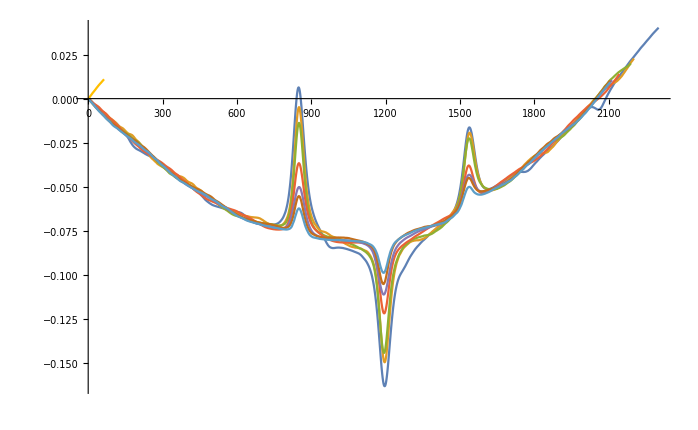

```mathematica
ListPlot[
{signals⟦1⟧-signals⟦1⟧⟦1⟧,
 signals⟦2⟧⟦x2-x1;;⟧-signals⟦2⟧⟦x2-x1;;⟧⟦1⟧, 
signals⟦3⟧⟦x3-x1;;⟧-signals⟦3⟧⟦x3-x1;;⟧⟦1⟧, 
signals⟦4⟧⟦x4-x1;;⟧-signals⟦4⟧⟦x4-x1;;⟧⟦1⟧,
signals⟦5⟧⟦x5-x1;;⟧-signals⟦5⟧⟦x5-x1;;⟧⟦1⟧, 
signals⟦6⟧⟦x6-x1;;⟧-signals⟦6⟧⟦x6-x1;;⟧⟦1⟧, 
signals⟦7⟧⟦x7-x1;;⟧-signals⟦7⟧⟦x7-x1;;⟧⟦1⟧, 
signals⟦8⟧⟦785-x1;;⟧-signals⟦8⟧⟦785-x1;;⟧⟦1⟧}
, Joined->True]
```

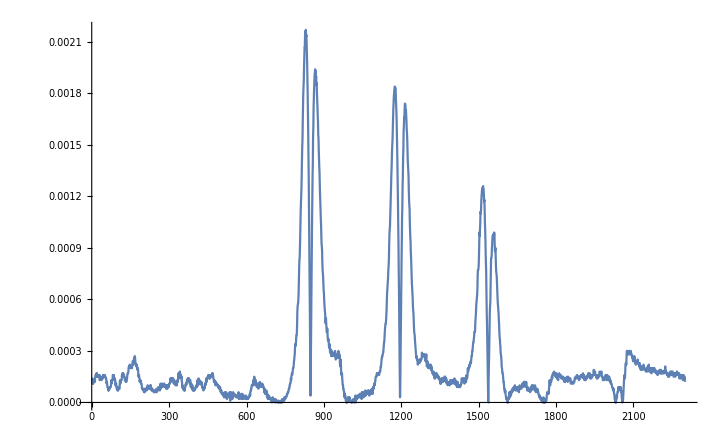

```mathematica
f  = signals⟦1⟧;
f1 = f⟦2;;⟧;
f2 = f⟦;;-2⟧;
f0 = f2-f1;
ListPlot[Abs@f0, PlotRange->Full, Joined->True]
```